## BC_CumulativeBeta.nb: Provide an elastic map and calculate cumulative beta curves for different node sequences and different node modes. This notebook is needed for ES_Superlattice.nb and others. INSTRUCTIONS: Run common_funs, ChooseTmat, then this.

## User choices

```mathematica
ComputeNM2=True;
ComputeNM3=True;
```

```mathematica
PrintFigures=False;
```

```mathematica
mdir
odir=FileNameJoin[{mdir,"pdf_print"}]
```

/Users/carltape/mma/elasticity

/Users/carltape/mma/elasticity/pdf_print

#### Σn gives the sequence of path nodes.

```mathematica
domain[Σn_]:=Range[nMax[Σn]];
range[Σn_]:=Σn/@domain[Σn];
```

#### MONO-ORTH-TET-XISO-ISO (the BrowaeysChevrot path)

```mathematica
ΣnTETXISO[1]=TRIV;
ΣnTETXISO[2]=MONO;
ΣnTETXISO[3]=ORTH; 
ΣnTETXISO[4]=TET;  
ΣnTETXISO[5]=XISO;
ΣnTETXISO[6]=ISO;  
nMax[ΣnTETXISO]=6;
range[ΣnTETXISO]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### MONO-ORTH-TET-CUBE-ISO

```mathematica
ΣnTETCUBE[1]=TRIV;
ΣnTETCUBE[2]=MONO;
ΣnTETCUBE[3]=ORTH;
ΣnTETCUBE[4]=TET; 
ΣnTETCUBE[5]=CUBE;
ΣnTETCUBE[6]=ISO; 
nMax[ΣnTETCUBE]=6;
range[ΣnTETCUBE]
```

{TRIV,MONO,ORTH,TET,CUBE,ISO}

#### MONO-TRIG-CUBE-ISO

```mathematica
ΣnTRIGCUBE[1]=TRIV;
ΣnTRIGCUBE[2]=MONO;
ΣnTRIGCUBE[3]=TRIG;  
ΣnTRIGCUBE[4]=CUBE;
ΣnTRIGCUBE[5]=ISO;  
nMax[ΣnTRIGCUBE]=5;
range[ΣnTRIGCUBE]
```

{TRIV,MONO,TRIG,CUBE,ISO}

#### MONO-TRIG-XISO-ISO

```mathematica
ΣnTRIGXISO[1]=TRIV;
ΣnTRIGXISO[2]=MONO;
ΣnTRIGXISO[3]=TRIG;  
ΣnTRIGXISO[4]=XISO;
ΣnTRIGXISO[5]=ISO;  
nMax[ΣnTRIGXISO]=5;
range[ΣnTRIGXISO]
```

{TRIV,MONO,TRIG,XISO,ISO}

#### Choose Σn

```mathematica
Σn=ΣnTETCUBE;
```

```mathematica
Σn=ΣnTRIGCUBE;
```

```mathematica
Σn=ΣnTRIGXISO;
```

```mathematica
Σn=ΣnTETXISO;
```

```mathematica
ListΣ=range[Σn]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

#### Choose dt

```mathematica
dt=0.5;
```

## Section 1. Points on the path and points on the lattice. No elastic maps are involved.

```mathematica
ListSigmaAll={TRIV,MONO,ORTH,TET,XISO,ISO,TRIG,CUBE};
```

#### SYMMETRIC LATTICE Use this version for a more symmetric lattice, but not when you want beta curves.

```mathematica
ww=1.;ww=1.2;
NodePt[ISO]  :={0.,5-.5};   
NodePt[XISO]:={-1ww,4.};   
NodePt[TRIG]:={-1ww,3.};  
NodePt[CUBE]:={  1ww,4.};
NodePt[TET]  :={  1ww,3.};  
NodePt[ORTH]:={  1ww,2.};  
NodePt[MONO]:={0.,1+.5};  
NodePt[TRIV]:={0.,0+.5};  
NodePts=NodePt/@ListSigmaAll;
dummy;
```

#### ASYMMETRIC LATTICE (DEFAULT)

```mathematica
ww=1.;ww=1.2;
NodePt[ISO]  :={0.,5-.5};   
NodePt[XISO]:={-1ww,4.};   
NodePt[TRIG]:={-1ww,3.-.15};  (* -.15 is to discourage coincident points *)
NodePt[CUBE]:={  1ww,4.};
NodePt[TET]  :={  1ww,3.};  
NodePt[ORTH]:={  1ww,2.};  
NodePt[MONO]:={0.,1+.5};  
NodePt[TRIV]:={0.,0+.5};  
NodePts=NodePt/@ListSigmaAll;
dummy;
```

```mathematica
xyIsNodePt[{x_,y_}]:=MemberQ[NodePts,{x,y}];   (* A statement, either true or false *)
```

#### Example

```mathematica
xyIsNodePt[{0.,1.5}]
xyIsNodePt[{0.,1.7}]
```

True

False

```mathematica
ΣofNodePt[NodePtIn_]:=Select[ListSigmaAll,NodePt[#]==NodePtIn&][[1]];
```

```mathematica
ΣofNodePt[NodePt[#]]==#&/@ListSigmaAll
```

{True,True,True,True,True,True,True,True}

```mathematica
LatticeBlank:={Arrowheads[.0008],Thickness[.0015],Dashing[{.013,.013}],
{Arrow[{NodePt[TRIV],NodePt[MONO]},.25]},  (* from TRIV to MONO *)
{Arrow[{NodePt[MONO],NodePt[ORTH]},.25]},  (* from MONO to ORTH *)
{Arrow[{NodePt[ORTH],NodePt[TET]},   .2]},   (* from ORTH *)
{Arrow[{NodePt[TET],  NodePt[CUBE]},.2]},   (* from TET to CUBE *)
{Arrow[{NodePt[TRIG],NodePt[XISO]},.2]},   (* from TRIG to XISO *)
{Arrow[{NodePt[TET],  NodePt[XISO]},.3]},   (* from TET to XISO *)
{Arrow[{NodePt[TRIG],NodePt[CUBE]},.3]},   (* from TRIG to CUBE *)
{Arrow[{NodePt[MONO],NodePt[TRIG]},.3]},   (* from MONO to TRIG *)
{Arrow[{NodePt[CUBE],NodePt[ISO]},.25]},   (* from CUBE to ISO *)
{Arrow[{NodePt[XISO],NodePt[ISO]},.25]}       (* from XISO to ISO *)
};
```

#### Examples.

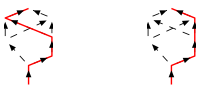

```mathematica
GraphicsRow[{
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnTETXISO[#]]&/@domain[ΣnTETXISO]]}}],
Graphics[{LatticeBlank,
{Red,Line[NodePt[ΣnTETCUBE[#]]&/@domain[ΣnTETCUBE]]}}]},ImageSize->200,Spacings->150]
```

#### Points on the path.

```mathematica
PointsOnPath[Σn_,dt_]:=UnsortedUnion[Flatten[Table[Table[(1-t) NodePt[Σn[j]]+t NodePt[Σn[j+1]],{t,0,1,dt}],{j,1,nMax[Σn]-1}],1]];
position[point_,dt_]:=Position[AllPoints[dt],point][[1,1]];path[Σn_,dt_]:=position[#,dt]&/@PointsOnPath[Σn,dt]
```

#### Σpairs specifies the segments of the lattice to put points on.

```mathematica
Σpairs={{TRIV,MONO},{MONO,ORTH},{MONO,TRIG},{ORTH,TET},{TET,XISO},{TET,CUBE},{XISO,ISO},{TRIG,CUBE},{TRIG,XISO},{CUBE,ISO}};
```

#### Example

```mathematica
Graphics[{LatticeBlank,
{Blue,Thickness[.02],Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

#### Colors (see ChooseTmat.nb).

```mathematica
(*HueOfΣ[TRIV]=Gray;                       BetaText[TRIV]="β_TRIV";
HueOfΣ[MONO]=Black;                     BetaText[MONO]="β_MONO";
HueOfΣ[ORTH]=Purple;                   BetaText[ORTH]="β_ORTH";
HueOfΣ[TET]  =Blue;                        BetaText[TET]  ="β_TET";
HueOfΣ[CUBE]=Orange;                   BetaText[CUBE]="β_CUBE";
HueOfΣ[XISO]=Hue[.5,1,.7];  BetaText[XISO]="β_XISO";
HueOfΣ[ISO]  =Red;                          BetaText[ISO]   ="β_ISO";
HueOfΣ[TRIG]=Cyan;                       BetaText[TRIG] ="β_TRIG";*)
```

## Densify the maps on the Σpairs segments.

#### The point command is set up so that point[ {0, {Σ_1, Σ_2} } ] = NodePt[Σ_1] point[ {1, {Σ_1, Σ_2} } ] = NodePt[Σ_2]

```mathematica
point[{t_,{Σ1_,Σ2_}}]:=(1-t) NodePt[Σ1]+t NodePt[Σ2];
UnsortedPointsWithTandΣpairs[dt_]:=Flatten[Table[{point[{t,#}],t,#},{t,0,1,dt}]&/@Σpairs,1];
PointsWithTandΣpairs[dt_]:=Sort[UnsortedPointsWithTandΣpairs[dt],OrderedQ[{#1[[1]],#2[[1]]}]&];
AllPoints[dt_]:=UnsortedUnion[#[[1]]&/@PointsWithTandΣpairs[dt]];
```

```mathematica
point[{0,{Σ1,Σ2}}]== NodePt[Σ1]
point[{1,{Σ1,Σ2}}]== NodePt[Σ2]
```

True

True

#### Example.

```mathematica
(* dt=.5;*)
Graphics[{LatticeBlank,
{Blue,Thickness[.015],PointSize[.05],
Point/@AllPoints[dt],
Line[{NodePt[#[[1]]],NodePt[#[[2]]]}]}&/@Σpairs},ImageSize->100]
```

-Graphics-

#### Examples.

```mathematica
(* dt=.5;*)
ColumnForm[AllPoints[dt]]
Length[%[[1]]]
```

{-1.2,2.85}
{-1.2,3.425}
{-1.2,4.}
{-0.6,2.175}
{-0.6,4.25}
{0.,0.5}
{0.,1.}
{0.,1.5}
{0.,3.425}
{0.,3.5}
{0.,4.5}
{0.6,1.75}
{0.6,4.25}
{1.2,2.}
{1.2,2.5}
{1.2,3.}
{1.2,3.5}
{1.2,4.}

18

```mathematica
PathSegments[Σn_]:=Table[{Σn[i],Σn[i+1]},{i,nMax[Σn]-1}];
```

```mathematica
PathSegments[ΣnTETXISO]
PathSegments[ΣnTRIGCUBE]
```

{{TRIV,MONO},{MONO,ORTH},{ORTH,TET},{TET,XISO},{XISO,ISO}}

{{TRIV,MONO},{MONO,TRIG},{TRIG,CUBE},{CUBE,ISO}}

```mathematica
PtTΣ1Σ2Triples[pt_,dt_]:=Select[PointsWithTandΣpairs[dt],#[[1]]==pt &]
```

```mathematica
ColumnForm[Table[PtTΣ1Σ2Triples[AllPoints[dt][[jj]],dt],{jj,Length[AllPoints[dt]]}]]
Length[%[[1]]]
```

{{{-1.2,2.85},1.,{MONO,TRIG}},{{-1.2,2.85},0.,{TRIG,CUBE}},{{-1.2,2.85},0.,{TRIG,XISO}}}
{{{-1.2,3.425},0.5,{TRIG,XISO}}}
{{{-1.2,4.},1.,{TET,XISO}},{{-1.2,4.},0.,{XISO,ISO}},{{-1.2,4.},1.,{TRIG,XISO}}}
{{{-0.6,2.175},0.5,{MONO,TRIG}}}
{{{-0.6,4.25},0.5,{XISO,ISO}}}
{{{0.,0.5},0.,{TRIV,MONO}}}
{{{0.,1.},0.5,{TRIV,MONO}}}
{{{0.,1.5},1.,{TRIV,MONO}},{{0.,1.5},0.,{MONO,ORTH}},{{0.,1.5},0.,{MONO,TRIG}}}
{{{0.,3.425},0.5,{TRIG,CUBE}}}
{{{0.,3.5},0.5,{TET,XISO}}}
{{{0.,4.5},1.,{XISO,ISO}},{{0.,4.5},1.,{CUBE,ISO}}}
{{{0.6,1.75},0.5,{MONO,ORTH}}}
{{{0.6,4.25},0.5,{CUBE,ISO}}}
{{{1.2,2.},1.,{MONO,ORTH}},{{1.2,2.},0.,{ORTH,TET}}}
{{{1.2,2.5},0.5,{ORTH,TET}}}
{{{1.2,3.},1.,{ORTH,TET}},{{1.2,3.},0.,{TET,XISO}},{{1.2,3.},0.,{TET,CUBE}}}
{{{1.2,3.5},0.5,{TET,CUBE}}}
{{{1.2,4.},1.,{TET,CUBE}},{{1.2,4.},1.,{TRIG,CUBE}},{{1.2,4.},0.,{CUBE,ISO}}}

18

```mathematica
UniqueTΣ1Σ2PtTriple[pt_,dt_,Σn_]:=If[Length[PtTΣ1Σ2Triples[pt,dt]]==1,PtTΣ1Σ2Triples[pt,dt][[1]],
If[Select[PtTΣ1Σ2Triples[pt,dt],MemberQ[PathSegments[Σn],#[[3]]]&]!={},Select[PtTΣ1Σ2Triples[pt,dt],MemberQ[PathSegments[Σn],#[[3]]]&&#[[2]]==1.&][[1]],
If[Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==1.&]!={},Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==1.&][[1]],
Select[PtTΣ1Σ2Triples[pt,dt],#[[2]]==0.&]]]];
```

```mathematica
dt
range[Σn]
ColumnForm[{PaddedForm[position[#,dt],2],
PaddedForm[#,{3,2}]&/@UniqueTΣ1Σ2PtTriple[#,dt,Σn][[1]],
PaddedForm[UniqueTΣ1Σ2PtTriple[#,dt,Σn][[2]],{2,1}],
UniqueTΣ1Σ2PtTriple[#,dt,Σn][[3]]}&/@AllPoints[dt]]
```

0.5

{TRIV,MONO,ORTH,TET,XISO,ISO}

{  1,{-1.20, 2.85}, 1.0,{MONO,TRIG}}
{  2,{-1.20, 3.43}, 0.5,{TRIG,XISO}}
{  3,{-1.20, 4.00}, 1.0,{TET,XISO}}
{  4,{-0.60, 2.18}, 0.5,{MONO,TRIG}}
{  5,{-0.60, 4.25}, 0.5,{XISO,ISO}}
{  6,{ 0.00, 0.50}, 0.0,{TRIV,MONO}}
{  7,{ 0.00, 1.00}, 0.5,{TRIV,MONO}}
{  8,{ 0.00, 1.50}, 1.0,{TRIV,MONO}}
{  9,{ 0.00, 3.43}, 0.5,{TRIG,CUBE}}
{ 10,{ 0.00, 3.50}, 0.5,{TET,XISO}}
{ 11,{ 0.00, 4.50}, 1.0,{XISO,ISO}}
{ 12,{ 0.60, 1.75}, 0.5,{MONO,ORTH}}
{ 13,{ 0.60, 4.25}, 0.5,{CUBE,ISO}}
{ 14,{ 1.20, 2.00}, 1.0,{MONO,ORTH}}
{ 15,{ 1.20, 2.50}, 0.5,{ORTH,TET}}
{ 16,{ 1.20, 3.00}, 1.0,{ORTH,TET}}
{ 17,{ 1.20, 3.50}, 0.5,{TET,CUBE}}
{ 18,{ 1.20, 4.00}, 1.0,{TET,CUBE}}

#### See the difference between the Σ pairs at the CUBE node in the two diagrams .

```mathematica
LatticeWithPts[dt_,Σn_]:=Graphics[{LatticeBlank,
If[Σn=!={},{Red,PointSize[.035],Line[PointsOnPath[Σn,dt]],Point/@PointsOnPath[Σn,dt]},{}],
PointSize[.02],
Point/@AllPoints[dt],
(* integer text label *)
Text[Style[position[#,dt],10],#+{.15,0}]&/@AllPoints[dt],
(* use this more detailed text for debugging *)
If[False,Text[Style[Row[UniqueTΣ1Σ2PtTriple[#,dt,Σn],"    "],10],#+{.9,0}]&/@NodePts ],
If[False,{Text[Style[ΣofNodePt[#],10],# +sign[#[[1]]]{.7,0}]&/@Select[NodePts ,#!=NodePt[ISO]&],
Text[Style[ISO,10],NodePt[ISO]+{0,0.3}]}]
},
ImageSize->250]
```

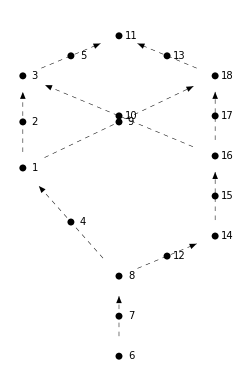

```mathematica
LatticeWithPts[dt,{}]
```

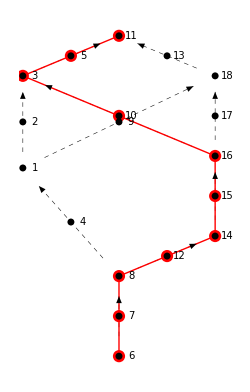

```mathematica
LatticeWithPts[dt,Σn]
```

```mathematica
LatticeWithPtsSigmas[Σn_]:=
Graphics[{LatticeBlank,
{Red,PointSize[.06],
Line[PointsOnPath[Σn,1]],
Point/@PointsOnPath[Σn,1]},  (* points on the red path *)
PointSize[.05],
Point/@AllPoints[1],
(* Sigmas *)
Text[Style[ΣofNodePt[#],10],# +sign[#[[1]]]{0.6,0}]&/@Select[NodePts ,#!=NodePt[ISO]&],
Text[Style[ISO,10],NodePt[ISO]+{0,0.3}]
},
ImageSize->150]
```

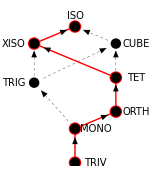

```mathematica
LatticeWithPtsSigmas[Σn]
```

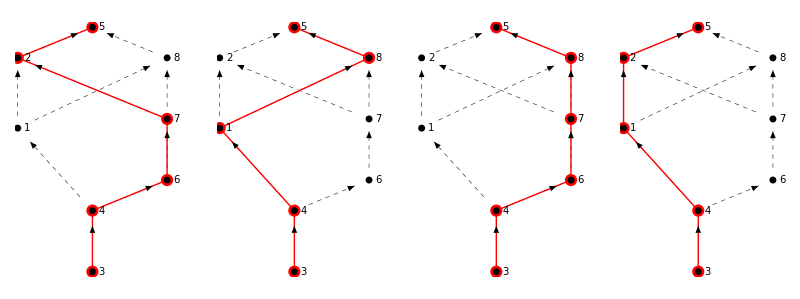

```mathematica
dtx=1;
GraphicsRow[{LatticeWithPts[dtx,ΣnTETXISO],LatticeWithPts[dtx,ΣnTRIGCUBE],LatticeWithPts[dtx,ΣnTETCUBE],LatticeWithPts[dtx,ΣnTRIGXISO]},Spacings->10,ImageSize->800]
```

```mathematica
TandΣpair[pt_,dt_]:=Select[PointsWithTandΣpairs[dt],#[[2]]==pt &][[1,1]];   
TofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[2]];
Σ1ofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3,1]];
Σ2ofPt[pt_,dt_,Σn_]:=UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3,2]];
NodePtsOfPt[pt_,dt_,Σn_]:=NodePt/@UniqueTΣ1Σ2PtTriple[pt,dt,Σn][[3]] (* points, not symmetry clases *)
```

#### Example.

{-0.6,2.175}

0.5

{MONO,TRIG}

{{0.,1.5},{-1.2,2.85}}

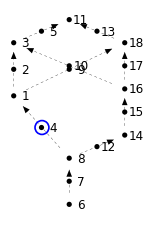

```mathematica
(* dt=.5; *)
pt=AllPoints[dt][[4]]  (* blue circle in diagram *)
TofPt[pt,dt,Σn]
{Σ1ofPt[pt,dt,Σn],Σ2ofPt[pt,dt,Σn]}
NodePtsOfPt[pt,dt,Σn]
Graphics[{LatticeBlank,
{Blue,Thickness[.008],Circle[pt,.15]},
PointSize[.025],
Point/@AllPoints[dt],
Text[Style[position[#,dt],12],#+{.25,0}]&/@AllPoints[dt]},ImageSize->150]
```

#### Example. These are the points on the path:

```mathematica
(* dt=.5 *)
range[Σn]
PointsOnPath[Σn,dt]
Length[%]
```

{TRIV,MONO,ORTH,TET,XISO,ISO}

{{0.,0.5},{0.,1.},{0.,1.5},{0.6,1.75},{1.2,2.},{1.2,2.5},{1.2,3.},{0.,3.5},{-1.2,4.},{-0.6,4.25},{0.,4.5}}

11

#### The main points figure (defined above), but still no elastic maps involved.

```mathematica
LatticeWithPtsText[dt_,Σn_]:=(Print["dt = ",dt];
Print["Σn values are ",range[Σn]];
Print["All points are ",AllPoints[dt]];
Print["Number of all points is ",Length[AllPoints[dt]]];
Print["path[Σn,dt] (red) is ",path[Σn,dt]];
Print["Points on red path are ",PointsOnPath[Σn,dt]];
Print["Number of points on red path is ",Length[PointsOnPath[Σn,dt]]];)
```

#### Lattice example:

```mathematica
LatticeWithPtsText[dt,Σn]
LatticeWithPts[dt,Σn]
```

dt = 0.5

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

All points are {{-1.2,2.85},{-1.2,3.425},{-1.2,4.},{-0.6,2.175},{-0.6,4.25},{0.,0.5},{0.,1.},{0.,1.5},{0.,3.425},{0.,3.5},{0.,4.5},{0.6,1.75},{0.6,4.25},{1.2,2.},{1.2,2.5},{1.2,3.},{1.2,3.5},{1.2,4.}}

Number of all points is 18

path[Σn,dt] (red) is {6,7,8,12,14,15,16,10,3,5,11}

Points on red path are {{0.,0.5},{0.,1.},{0.,1.5},{0.6,1.75},{1.2,2.},{1.2,2.5},{1.2,3.},{0.,3.5},{-1.2,4.},{-0.6,4.25},{0.,4.5}}

Number of points on red path is 11

-Graphics-

#### As functions of integer j. The integer j will give the point (j, 0) on the horizontal axis in the Beta curve diagrams. It runs over 1, 2, 3, ..., Length[path]. Not needed for the cumulative diagram or for the Lattice file. It does not involve elastic maps.

#### ΣofPt[pt, dt, Σn] is the symmetry class for the elastic map at pt, but only if pt is a node.

```mathematica
ΣofPt[pt_,dt_,Σn_]:=If[TofPt[pt,dt,Σn]==0.,Σ1ofPt[pt,dt,Σn],
                                             If[TofPt[pt,dt,Σn]==1.,Σ2ofPt[pt,dt,Σn]," "]];   
PathPtOfJ[j_,Σn_,dt_]:=PointsOnPath[Σn,dt][[j]];  
jIsNode[j_,Σn_,dt_]:=xyIsNodePt[PathPtOfJ[j,Σn,dt]];  (* A statement, either true or false *)
JlistForNodes[Σn_,dt_]:=Select[Range[Length[PointsOnPath[Σn,dt]]],jIsNode[#,Σn,dt]&];
ΣofJ[j_,Σn_,dt_]:=ΣofPt[PathPtOfJ[j,Σn,dt],dt,Σn];
```

#### Example.

```mathematica
Print["dt = ",dt]
Print["Σn values are ",range[Σn]]
PathPtOfJ[4,Σn,dt]
jIsNode[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
JlistForNodes[Σn,dt]
ΣofJ[#,Σn,dt]&/@Range[Length[PointsOnPath[Σn,dt]]]
```

dt = 0.5

Σn values are {TRIV,MONO,ORTH,TET,XISO,ISO}

{0.6,1.75}

{True,False,True,False,True,False,True,False,True,False,True}

{1,3,5,7,9,11}

{TRIV, ,MONO, ,ORTH, ,TET, ,XISO, ,ISO}

## Section 2. Elastic maps at nodes only. There is no dt at this stage.

#### Choose Tmat

```mathematica
Tmat=TmatMar17;
```

```mathematica
Tmat=TmatIgel;
```

```mathematica
Tmat=TmatFrancois;
```

```mathematica
Tmat=TmatAminzadehBukov0p1;
```

```mathematica
Tmat=TmatAminzadehGrimsel0p1;
```

```mathematica
Tmat=TmatBrownAbramson2016s9; (* s1, ..., s9 *)
```

```mathematica
Tmat=TmatLokajicekWG600hp; (* 100 or 600; lp or hp *)
```

```mathematica
Tmat=TmatVestrum;
```

```mathematica
Tmat=TmatArtsVosges;
```

```mathematica
Tmat=TmatJi1994NunivakIsland; (* NunivakIsland, CastleRock, AlligatorLake *)
```

```mathematica
Tmat=TmatSSA2023;
```

```mathematica
Tmat=TmatMar17mod;
```

```mathematica
Tmat=TmatBColivine; (* enstatite, olivine *)
```

```mathematica
Tmat=TmatBrownAn00Pert;
```

```mathematica
Tmat=TmatRussell;
```

```mathematica
Tmat=TmatIsmailMainpriceKimberlite; (* Total, Ridge, Subduction, Kimberlite *)
```

```mathematica
Tmat=TmatFrancoisSipo;  (* Oak, Beech, Sipo, Vosges *)
```

```mathematica
Tmat=TmatBrownAn00; (* 00, 25, 37, 48, 60, 67, 78, 96 *)
```

#### Check for symmetry. Display output.

```mathematica
Tmat==Transpose[Tmat]
If[!(Tmat==Transpose[Tmat]),MatrixForm[Tmat-Transpose[Tmat]]]
MatrixNote[Tmat]
PrintVoigt[Tmat]
```

True

T is BrownAn00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

#### SmatOfΣ[Σ, Tmat, Σn, nm] is the elastic map at node Σ for node mode nm. So it should have symmetry Σ The input Σn is only needed for nm = nm3. You can enter the command SmatOfΣ, but do not try to evaluate it unless you have run the appropriate OutputFor, described momentarily.

#### This is the command that allows us to unify everything.

```mathematica
SmatOfΣ[Σ_,Tmat_,dummy_,nm1]:=ProjToVSigOfU[Tmat,UforNM1,Σ];
SmatOfΣ[Σ_,Tmat_,dummy_,nm2]:=Closest[Tmat,Σ];
SmatOfΣ[Σ_,Tmat_,Σn_,       nm3]:=ClosestToPrior[Σ,Tmat,Σn];
```

```mathematica
TextNodeMode[nm1]="Node mode nm1: P(T,𝒱_Σ(U))";
TextNodeMode[nm2]="Node mode nm2: Closest to Tmat";
TextNodeMode[nm3]="Node mode nm3: Closest to prior";
```

#### Angle between the elastic maps at adjacent nodes.

```mathematica
AngleToNextFrom[n_,Tmat_,Σn_,nm_]:=AngleMatrix[SmatOfΣ[Σn[n],Tmat,Σn,nm],SmatOfΣ[Σn[n+1],Tmat,Σn,nm]];
```

#### For nm2.

```mathematica
MatrixNote[Tmat]
(* OutputFor[Tmat,#]&/@ListSigmaAll *)
MinimizationFacts[Tmat,#]&/@ListSigmaAll
```

T is BrownAn00

𝒯_TRIV = 𝒯

d_TRIV^T = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯) = 0           ''

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T | β_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 19.3941 | 3.77^∘ |   1.682227 |   0.319894 |   2.331993

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.68223,0.319894,2.33199} = {96.4^∘,18.3^∘,133.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.239703 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 19.394 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0.066 = 3.77^o (Angle between T and 𝒯_MONO)

𝒱_MONO(U_0) contains a closest map to T in 𝒯_MONO

P(T, 𝒱_MONO(U_0))= (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_(θ,σ,ϕ):

seed | d_ORTH^T | β_ORTH^T |   θ_0 |   σ_0 |    ϕ_0
0 | 32.9751 | 6.42^∘ |   1.479286 |  -1.418119 |   0.768554

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.47929,-1.41812,0.768554} = {84.8^∘,-81.3^∘,44.^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.994223 | -0.0865168 | 0.0635195
0.0185598 | 0.721479 | 0.692188
-0.105714 | -0.68701 | 0.718917)  (One of at least 24 ORTH-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

d_ORTH^T = d(T, P(T,𝒱_ORTH(U_0))) = 32.975 (Distance between T and 𝒯_ORTH)

β_ORTH^T = sin^-1(d_ORTH^T/|T|) = 0.112 = 6.42^o (Angle between T and 𝒯_ORTH)

𝒱_ORTH(U_0) contains a closest map to T in 𝒯_ORTH

P(T, 𝒱_ORTH(U_0))= (47.2694 | -3.19958 | -1.00821 | -9.32212 | 11.7379 | -8.26656
-3.19958 | 62.3442 | 2.27011 | -5.04078 | -11.271 | 7.50877
-1.00821 | 2.27011 | 60.5007 | -2.56615 | -0.102698 | -2.19801
-9.32212 | -5.04078 | -2.56615 | 95.9546 | 48.8761 | 34.9099
11.7379 | -11.271 | -0.102698 | 48.8761 | 148.264 | -19.294
-8.26656 | 7.50877 | -2.19801 | 34.9099 | -19.294 | 189.267)  (a closest elastic map to T having symmetry at least ORTH)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TET^T | β_TET^T |   θ_0 |   σ_0 |    ϕ_0
0 | 40.302 | 7.86^∘ |   0.045499 |   0.027473 |   1.662707

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.0454989,0.0274727,1.66271} = {2.6^∘,1.6^∘,95.3^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.0929013 | -0.0429474 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)  (One of at least 16 TET-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

d_TET^T = d(T, P(T,𝒱_TET(U_0))) = 40.302 (Distance between T and 𝒯_TET)

β_TET^T = sin^-1(d_TET^T/|T|) = 0.137 = 7.86^o (Angle between T and 𝒯_TET)

𝒱_TET(U_0) contains a closest map to T in 𝒯_TET

P(T, 𝒱_TET(U_0))= (47.8734 | -0.0381237 | -1.44566 | 3.29296 | 5.70502 | 0.297458
-0.0381237 | 61.4644 | 0.409217 | -4.57872 | -10.1088 | 6.53319
-1.44566 | 0.409217 | 60.3897 | -2.89207 | -3.8001 | -3.22392
3.29296 | -4.57872 | -2.89207 | 95.5029 | 47.8919 | 35.3307
5.70502 | -10.1088 | -3.8001 | 47.8919 | 149.103 | -20.1349
0.297458 | 6.53319 | -3.22392 | 35.3307 | -20.1349 | 189.267)  (a closest elastic map to T having symmetry at least TET)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_XISO^T | β_XISO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 94.1024 | 18.62^∘ |   2.763968 |  -3.049047 |   3.009543

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {2.76397,-3.04905,3.00954} = {158.4^∘,-174.7^∘,172.4^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.883433 | 0.452291 | -0.12239
0.449842 | 0.891788 | 0.0485472
0.131103 | -0.0121678 | -0.991294)  (One of at least ∞ XISO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

d_XISO^T = d(T, P(T,𝒱_XISO(U_0))) = 94.102 (Distance between T and 𝒯_XISO)

β_XISO^T = sin^-1(d_XISO^T/|T|) = 0.325 = 18.62^o (Angle between T and 𝒯_XISO)

𝒱_XISO(U_0) contains a closest map to T in 𝒯_XISO

P(T, 𝒱_XISO(U_0))= (50.3841 | -1.8222 | -3.82051 | 1.65935 | 8.438 | -1.49042
-1.8222 | 54.2551 | 1.3059 | 3.65501 | -21.2726 | 3.75741
-3.82051 | 1.3059 | 80.8566 | 0.0129359 | 1.37423 | -0.184014
1.65935 | 3.65501 | 0.0129359 | 80.8581 | 1.4597 | -0.195458
8.438 | -21.2726 | 1.37423 | 1.4597 | 147.979 | -17.4156
-1.49042 | 3.75741 | -0.184014 | -0.195458 | -17.4156 | 189.267)  (a closest elastic map to T having symmetry at least XISO)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TRIG^T | β_TRIG^T |   θ_0 |   σ_0 |    ϕ_0
0 | 82.3728 | 16.23^∘ |   0.229040 |  -0.867254 |   1.337359

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.22904,-0.867254,1.33736} = {13.1^∘,-49.7^∘,76.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)  (One of at least 12 TRIG-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

d_TRIG^T = d(T, P(T,𝒱_TRIG(U_0))) = 82.373 (Distance between T and 𝒯_TRIG)

β_TRIG^T = sin^-1(d_TRIG^T/|T|) = 0.283 = 16.23^o (Angle between T and 𝒯_TRIG)

𝒱_TRIG(U_0) contains a closest map to T in 𝒯_TRIG

P(T, 𝒱_TRIG(U_0))= (86.1583 | -20.7848 | -27.4637 | -18.0406 | 7.28212 | -3.65734
-20.7848 | 63.5007 | 17.858 | -2.53608 | -10.5831 | -15.6879
-27.4637 | 17.858 | 70.0111 | 7.84699 | 2.43911 | -14.98
-18.0406 | -2.53608 | 7.84699 | 81.7222 | 21.7491 | 30.3818
7.28212 | -10.5831 | 2.43911 | 21.7491 | 112.941 | -17.3459
-3.65734 | -15.6879 | -14.98 | 30.3818 | -17.3459 | 189.267)  (a closest elastic map to T having symmetry at least TRIG)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_(θ,σ,ϕ):

seed | d_CUBE^T | β_CUBE^T |   θ_0 |   σ_0 |    ϕ_0
0 | 106.21 | 21.12^∘ |   1.664704 |  -1.471758 |   1.534718

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.6647,-1.47176,1.53472} = {95.4^∘,-84.3^∘,87.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.990381 | -0.101807 | -0.093709
0.0968614 | 0.0264644 | 0.994946
-0.0988123 | -0.994452 | 0.036071)  (One of at least 24 CUBE-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

d_CUBE^T = d(T, P(T,𝒱_CUBE(U_0))) = 106.21 (Distance between T and 𝒯_CUBE)

β_CUBE^T = sin^-1(d_CUBE^T/|T|) = 0.369 = 21.12^o (Angle between T and 𝒯_CUBE)

𝒱_CUBE(U_0) contains a closest map to T in 𝒯_CUBE

P(T, 𝒱_CUBE(U_0))= (56.1586 | -0.249516 | -0.565842 | 3.02019 | 3.0469 | 0
-0.249516 | 58.556 | -1.26106 | 6.12452 | -11.588 | 0
-0.565842 | -1.26106 | 58.2948 | -12.4577 | 0.216087 | 0
3.02019 | 6.12452 | -12.4577 | 120.193 | 1.03807 | 0
3.0469 | -11.588 | 0.216087 | 1.03807 | 121.131 | 0
0 | 0 | 0 | 0 | 0 | 189.267)  (a closest elastic map to T having symmetry at least CUBE)

{Null,Null,Null,Null,Null,Null,Null,Null}

#### The matrices UT[Tmat, Σ] produced by MinimizationFacts above.

```mathematica
MatrixNote[Tmat]
{#,MatrixForm[UT[Tmat,#]]}&/@ListSigmaAll
```

T is BrownAn00

{{TRIV,(0.0168331 | -0.0346641 | 0.999257
0.566642 | 0.823744 | 0.0190301
-0.823792 | 0.565901 | 0.0335084)},{MONO,(-0.239703 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)},{ORTH,(0.994223 | -0.0865168 | 0.0635195
0.0185598 | 0.721479 | 0.692188
-0.105714 | -0.68701 | 0.718917)},{TET,(-0.0929013 | -0.0429474 | 0.994749
0.0232679 | 0.998703 | 0.0452912
-0.995403 | 0.0273533 | -0.0917815)},{XISO,(-0.883433 | 0.452291 | -0.12239
0.449842 | 0.891788 | 0.0485472
0.131103 | -0.0121678 | -0.991294)},{ISO,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)},{TRIG,(0.318873 | 0.0249105 | 0.94747
-0.708665 | 0.670078 | 0.220885
-0.629376 | -0.741873 | 0.231323)},{CUBE,(0.990381 | -0.101807 | -0.093709
0.0968614 | 0.0264644 | 0.994946
-0.0988123 | -0.994452 | 0.036071)}}

#### For nm3. This paragraph should be run for each path Σn that you want. Save the output for comparison later.

```mathematica
Σn
Σn/@domain[Σn]
Σn[3]
PriorΣ[Σn[3],Σn]
NextΣ[Σn[3],Σn]
```

ΣnTETXISO

{TRIV,MONO,ORTH,TET,XISO,ISO}

ORTH

MONO

TET

#### Needed if you have not run the nm2 above:

```mathematica
MatrixNote[Tmat]
range[Σn]
MinimizationFacts[Tmat,Σn[1]]
```

T is BrownAn00

{TRIV,MONO,ORTH,TET,XISO,ISO}

𝒯_TRIV = 𝒯

d_TRIV^T = d(T, 𝒯) = 0 for all elastic maps T

β_TRIV^T = ∠(T, 𝒯) = 0           ''

#### This is subtle, in that each step is evaluating SmatOfΣ (via ClosestToPrior) for the next. If troubles occur, try going back to the AA file and reentering ClosestToPrior.

```mathematica
(* MatrixNote[Tmat]
range[Σn]
MinmizationFacts[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]]&/@Drop[range[Σn],-1] *)
```

#### COMPUTE nm3 FOR ALL PRE-CHOSEN NODE SEQUENCES (This takes time but provides the most flexibility for later.)

```mathematica
If[ComputeNM3,
Print[MatrixNote[Tmat]];
Print[range[ΣnTETXISO]];
MinimizationFacts[SmatOfΣ[#,Tmat,ΣnTETXISO,nm3],NextΣ[#,ΣnTETXISO]]&/@Drop[range[ΣnTETXISO],-1];]
```

T is BrownAn00

{TRIV,MONO,ORTH,TET,XISO,ISO}

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T | β_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 19.3941 | 3.77^∘ |   1.682227 |   0.319894 |   2.331993

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.68223,0.319894,2.33199} = {96.4^∘,18.3^∘,133.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.239702 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 19.394 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0.066 = 3.77^o (Angle between T and 𝒯_MONO)

𝒱_MONO(U_0) contains a closest map to T in 𝒯_MONO

P(T, 𝒱_MONO(U_0))= (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_(θ,σ,ϕ):

seed | d_ORTH^T | β_ORTH^T |   θ_0 |   σ_0 |    ϕ_0
0 | 26.7156 | 5.21^∘ |   0.013398 |   0.804573 |   1.673169

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.013398,0.804573,1.67317} = {0.8^∘,46.1^∘,95.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)  (One of at least 24 ORTH-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

d_ORTH^T = d(T, P(T,𝒱_ORTH(U_0))) = 26.716 (Distance between T and 𝒯_ORTH)

β_ORTH^T = sin^-1(d_ORTH^T/|T|) = 0.091 = 5.21^o (Angle between T and 𝒯_ORTH)

𝒱_ORTH(U_0) contains a closest map to T in 𝒯_ORTH

P(T, 𝒱_ORTH(U_0))= (47.3087 | -3.09908 | -1.05627 | -9.84992 | 11.085 | -8.30133
-3.09908 | 62.1997 | 2.3175 | -4.94367 | -10.8641 | 7.22046
-1.05627 | 2.3175 | 60.4795 | -2.21162 | 0.294031 | -1.79801
-9.84992 | -4.94367 | -2.21162 | 95.826 | 48.9018 | 34.886
11.085 | -10.8641 | 0.294031 | 48.9018 | 148.519 | -19.3664
-8.30133 | 7.22046 | -1.79801 | 34.886 | -19.3664 | 189.267)  (a closest elastic map to T having symmetry at least ORTH)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TET^T | β_TET^T |   θ_0 |   σ_0 |    ϕ_0
0 | 23.9577 | 4.69^∘ |   0.013398 |   0.019175 |   1.673169

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.013398,0.0191751,1.67317} = {0.8^∘,1.1^∘,95.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133274
-0.994582 | 0.0190736 | -0.102194)  (One of at least 16 TET-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

d_TET^T = d(T, P(T,𝒱_TET(U_0))) = 23.958 (Distance between T and 𝒯_TET)

β_TET^T = sin^-1(d_TET^T/|T|) = 0.082 = 4.69^o (Angle between T and 𝒯_TET)

𝒱_TET(U_0) contains a closest map to T in 𝒯_TET

P(T, 𝒱_TET(U_0))= (47.3843 | -0.315251 | -1.42524 | 2.43642 | 4.1673 | 0.095679
-0.315251 | 62.0514 | 0.103912 | -5.15905 | -10.8992 | 7.14088
-1.42524 | 0.103912 | 60.4942 | -0.675363 | -0.859383 | -0.931261
2.43642 | -5.15905 | -0.675363 | 95.4268 | 48.601 | 34.7455
4.1673 | -10.8992 | -0.859383 | 48.601 | 148.977 | -19.6439
0.095679 | 7.14088 | -0.931261 | 34.7455 | -19.6439 | 189.267)  (a closest elastic map to T having symmetry at least TET)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_XISO^T | β_XISO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 88.7118 | 17.69^∘ |   1.582234 |  -1.080641 |   1.551722

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.58223,-1.08064,1.55172} = {90.7^∘,-61.9^∘,88.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.882099 | -0.470925 | -0.0114358
0.0190697 | 0.0114422 | 0.999753
-0.470678 | -0.882099 | 0.0190736)  (One of at least ∞ XISO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

d_XISO^T = d(T, P(T,𝒱_XISO(U_0))) = 88.712 (Distance between T and 𝒯_XISO)

β_XISO^T = sin^-1(d_XISO^T/|T|) = 0.309 = 17.69^o (Angle between T and 𝒯_XISO)

𝒱_XISO(U_0) contains a closest map to T in 𝒯_XISO

P(T, 𝒱_XISO(U_0))= (53.9601 | 0.272518 | -0.0635837 | 2.55059 | 1.99914 | 0.66979
0.272518 | 77.7813 | -0.45593 | -0.0396237 | -0.0228675 | -0.00766149
-0.0635837 | -0.45593 | 53.8922 | -1.80307 | -0.724324 | -0.401581
2.55059 | -0.0396237 | -1.80307 | 132.655 | 31.6571 | 17.5514
1.99914 | -0.0228675 | -0.724324 | 31.6571 | 96.0444 | 10.1286
0.66979 | -0.00766149 | -0.401581 | 17.5514 | 10.1286 | 189.267)  (a closest elastic map to T having symmetry at least XISO)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 84.9089   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.31 = 17.77^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

```mathematica
If[ComputeNM3,
Print[MatrixNote[Tmat]];
Print[range[ΣnTRIGCUBE]];
MinimizationFacts[SmatOfΣ[#,Tmat,ΣnTRIGCUBE,nm3],NextΣ[#,ΣnTRIGCUBE]]&/@Drop[range[ΣnTRIGCUBE],-1];]
```

T is BrownAn00

{TRIV,MONO,TRIG,CUBE,ISO}

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T | β_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 19.3941 | 3.77^∘ |   1.682227 |   0.319894 |   2.331993

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.68223,0.319894,2.33199} = {96.4^∘,18.3^∘,133.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.239702 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 19.394 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0.066 = 3.77^o (Angle between T and 𝒯_MONO)

𝒱_MONO(U_0) contains a closest map to T in 𝒯_MONO

P(T, 𝒱_MONO(U_0))= (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TRIG^T | β_TRIG^T |   θ_0 |   σ_0 |    ϕ_0
0 | 81.7126 | 16.13^∘ |   0.294460 |   0.268627 |   1.382032

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.29446,0.268627,1.38203} = {16.9^∘,15.4^∘,79.2^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.0961012 | -0.327473 | 0.939961
0.30649 | 0.908185 | 0.285067
-0.94701 | 0.260693 | 0.187645)  (One of at least 12 TRIG-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

d_TRIG^T = d(T, P(T,𝒱_TRIG(U_0))) = 81.713 (Distance between T and 𝒯_TRIG)

β_TRIG^T = sin^-1(d_TRIG^T/|T|) = 0.281 = 16.13^o (Angle between T and 𝒯_TRIG)

𝒱_TRIG(U_0) contains a closest map to T in 𝒯_TRIG

P(T, 𝒱_TRIG(U_0))= (84.1964 | -27.9889 | -18.4114 | -17.6504 | 8.04716 | -3.85392
-27.9889 | 72.6521 | 17.8714 | 2.23431 | -10.4875 | -12.7076
-18.4114 | 17.8714 | 62.5913 | 3.11132 | 5.04276 | -19.3052
-17.6504 | 2.23431 | 3.11132 | 86.8668 | 23.7386 | 28.9004
8.04716 | -10.4875 | 5.04276 | 23.7386 | 108.027 | -18.6013
-3.85392 | -12.7076 | -19.3052 | 28.9004 | -18.6013 | 189.267)  (a closest elastic map to T having symmetry at least TRIG)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_(θ,σ,ϕ):

seed | d_CUBE^T | β_CUBE^T |   θ_0 |   σ_0 |    ϕ_0
0 | 75.8243 | 15.57^∘ |   1.191255 |   1.133761 |   0.824001

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.19125,1.13376,0.824001} = {68.3^∘,65.^∘,47.2^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.735012 | -0.621153 | 0.271895
0.602724 | -0.414832 | 0.681644
-0.310614 | 0.664894 | 0.67929)  (One of at least 24 CUBE-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

d_CUBE^T = d(T, P(T,𝒱_CUBE(U_0))) = 75.824 (Distance between T and 𝒯_CUBE)

β_CUBE^T = sin^-1(d_CUBE^T/|T|) = 0.272 = 15.57^o (Angle between T and 𝒯_CUBE)

𝒱_CUBE(U_0) contains a closest map to T in 𝒯_CUBE

P(T, 𝒱_CUBE(U_0))= (68.48 | -17.9586 | -11.1956 | -15.6443 | 7.31144 | 0
-17.9586 | 76.3562 | 19.8656 | -6.87882 | -7.47685 | 0
-11.1956 | 19.8656 | 71.7491 | -5.48608 | 15.5526 | 0
-15.6443 | -6.87882 | -5.48608 | 99.2085 | 3.41048 | 0
7.31144 | -7.47685 | 15.5526 | 3.41048 | 98.5396 | 0
0 | 0 | 0 | 0 | 0 | 189.267)  (a closest elastic map to T having symmetry at least CUBE)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 62.7752   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.233 = 13.33^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

```mathematica
If[ComputeNM3,
Print[MatrixNote[Tmat]];
Print[range[ΣnTETCUBE]];
MinimizationFacts[SmatOfΣ[#,Tmat,ΣnTETCUBE,nm3],NextΣ[#,ΣnTETCUBE]]&/@Drop[range[ΣnTETCUBE],-1];]
```

T is BrownAn00

{TRIV,MONO,ORTH,TET,CUBE,ISO}

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T | β_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 19.3941 | 3.77^∘ |   1.682227 |   0.319894 |   2.331993

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.68223,0.319894,2.33199} = {96.4^∘,18.3^∘,133.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.239702 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 19.394 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0.066 = 3.77^o (Angle between T and 𝒯_MONO)

𝒱_MONO(U_0) contains a closest map to T in 𝒯_MONO

P(T, 𝒱_MONO(U_0))= (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_(θ,σ,ϕ):

seed | d_ORTH^T | β_ORTH^T |   θ_0 |   σ_0 |    ϕ_0
0 | 26.7156 | 5.21^∘ |   0.013398 |   0.804573 |   1.673169

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.013398,0.804573,1.67317} = {0.8^∘,46.1^∘,95.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.0805105 | 0.0643378 | 0.994675
0.719521 | 0.694343 | 0.0133274
-0.689788 | 0.716762 | -0.102194)  (One of at least 24 ORTH-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

d_ORTH^T = d(T, P(T,𝒱_ORTH(U_0))) = 26.716 (Distance between T and 𝒯_ORTH)

β_ORTH^T = sin^-1(d_ORTH^T/|T|) = 0.091 = 5.21^o (Angle between T and 𝒯_ORTH)

𝒱_ORTH(U_0) contains a closest map to T in 𝒯_ORTH

P(T, 𝒱_ORTH(U_0))= (47.3087 | -3.09908 | -1.05627 | -9.84992 | 11.085 | -8.30133
-3.09908 | 62.1997 | 2.3175 | -4.94367 | -10.8641 | 7.22046
-1.05627 | 2.3175 | 60.4795 | -2.21162 | 0.294031 | -1.79801
-9.84992 | -4.94367 | -2.21162 | 95.826 | 48.9018 | 34.886
11.085 | -10.8641 | 0.294031 | 48.9018 | 148.519 | -19.3664
-8.30133 | 7.22046 | -1.79801 | 34.886 | -19.3664 | 189.267)  (a closest elastic map to T having symmetry at least ORTH)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TET^T | β_TET^T |   θ_0 |   σ_0 |    ϕ_0
0 | 23.9577 | 4.69^∘ |   0.013398 |   0.019175 |   1.673169

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.013398,0.0191751,1.67317} = {0.8^∘,1.1^∘,95.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133274
-0.994582 | 0.0190736 | -0.102194)  (One of at least 16 TET-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

d_TET^T = d(T, P(T,𝒱_TET(U_0))) = 23.958 (Distance between T and 𝒯_TET)

β_TET^T = sin^-1(d_TET^T/|T|) = 0.082 = 4.69^o (Angle between T and 𝒯_TET)

𝒱_TET(U_0) contains a closest map to T in 𝒯_TET

P(T, 𝒱_TET(U_0))= (47.3843 | -0.315251 | -1.42524 | 2.43642 | 4.1673 | 0.095679
-0.315251 | 62.0514 | 0.103912 | -5.15905 | -10.8992 | 7.14088
-1.42524 | 0.103912 | 60.4942 | -0.675363 | -0.859383 | -0.931261
2.43642 | -5.15905 | -0.675363 | 95.4268 | 48.601 | 34.7455
4.1673 | -10.8992 | -0.859383 | 48.601 | 148.977 | -19.6439
0.095679 | 7.14088 | -0.931261 | 34.7455 | -19.6439 | 189.267)  (a closest elastic map to T having symmetry at least TET)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_(θ,σ,ϕ):

seed | d_CUBE^T | β_CUBE^T |   θ_0 |   σ_0 |    ϕ_0
0 | 98.5233 | 19.72^∘ |   0.013398 |   0.019175 |   1.673169

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.013398,0.0191751,1.67317} = {0.8^∘,1.1^∘,95.9^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.102423 | -0.0114358 | 0.994675
0.0178033 | 0.999753 | 0.0133274
-0.994582 | 0.0190736 | -0.102194)  (One of at least 24 CUBE-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

d_CUBE^T = d(T, P(T,𝒱_CUBE(U_0))) = 98.523 (Distance between T and 𝒯_CUBE)

β_CUBE^T = sin^-1(d_CUBE^T/|T|) = 0.344 = 19.72^o (Angle between T and 𝒯_CUBE)

𝒱_CUBE(U_0) contains a closest map to T in 𝒯_CUBE

P(T, 𝒱_CUBE(U_0))= (56.1932 | -0.223413 | -0.0272703 | 1.37732 | 2.03077 | 0
-0.223413 | 58.8738 | -0.204851 | 6.64411 | -11.5552 | 0
-0.0272703 | -0.204851 | 56.1438 | -1.64069 | 0.193481 | 0
1.37732 | 6.64411 | -1.64069 | 122.256 | 1.16072 | 0
2.03077 | -11.5552 | 0.193481 | 1.16072 | 120.866 | 0
0 | 0 | 0 | 0 | 0 | 189.267)  (a closest elastic map to T having symmetry at least CUBE)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 73.2971   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.27 = 15.47^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

```mathematica
If[ComputeNM3,
Print[MatrixNote[Tmat]];
Print[range[ΣnTRIGXISO]];
MinimizationFacts[SmatOfΣ[#,Tmat,ΣnTRIGXISO,nm3],NextΣ[#,ΣnTRIGXISO]]&/@Drop[range[ΣnTRIGXISO],-1]]
```

T is BrownAn00

{TRIV,MONO,TRIG,XISO,ISO}

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_MONO^T | β_MONO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 19.3941 | 3.77^∘ |   1.682227 |   0.319894 |   2.331993

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {1.68223,0.319894,2.33199} = {96.4^∘,18.3^∘,133.6^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.239702 | -0.967502 | -0.0805105
-0.685702 | 0.110011 | 0.719521
-0.687281 | 0.227677 | -0.689788)  (One of at least ∞ MONO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

d_MONO^T = d(T, P(T,𝒱_MONO(U_0))) = 19.394 (Distance between T and 𝒯_MONO)

β_MONO^T = sin^-1(d_MONO^T/|T|) = 0.066 = 3.77^o (Angle between T and 𝒯_MONO)

𝒱_MONO(U_0) contains a closest map to T in 𝒯_MONO

P(T, 𝒱_MONO(U_0))= (48.5015 | -10.1159 | -7.74458 | -9.22251 | 9.37601 | -7.38876
-10.1159 | 61.7123 | 0.910195 | -8.9761 | -11.3441 | -3.2773
-7.74458 | 0.910195 | 59.1615 | -3.40581 | 4.3541 | -12.0748
-9.22251 | -8.9761 | -3.40581 | 96.5977 | 48.3338 | 35.6995
9.37601 | -11.3441 | 4.3541 | 48.3338 | 148.36 | -21.2519
-7.38876 | -3.2773 | -12.0748 | 35.6995 | -21.2519 | 189.267)  (a closest elastic map to T having symmetry at least MONO)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_(θ,σ,ϕ):

seed | d_TRIG^T | β_TRIG^T |   θ_0 |   σ_0 |    ϕ_0
0 | 81.7126 | 16.13^∘ |   0.294460 |   0.268627 |   1.382032

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.29446,0.268627,1.38203} = {16.9^∘,15.4^∘,79.2^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (0.0961012 | -0.327473 | 0.939961
0.30649 | 0.908185 | 0.285067
-0.94701 | 0.260693 | 0.187645)  (One of at least 12 TRIG-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

d_TRIG^T = d(T, P(T,𝒱_TRIG(U_0))) = 81.713 (Distance between T and 𝒯_TRIG)

β_TRIG^T = sin^-1(d_TRIG^T/|T|) = 0.281 = 16.13^o (Angle between T and 𝒯_TRIG)

𝒱_TRIG(U_0) contains a closest map to T in 𝒯_TRIG

P(T, 𝒱_TRIG(U_0))= (84.1964 | -27.9889 | -18.4114 | -17.6504 | 8.04716 | -3.85392
-27.9889 | 72.6521 | 17.8714 | 2.23431 | -10.4875 | -12.7076
-18.4114 | 17.8714 | 62.5913 | 3.11132 | 5.04276 | -19.3052
-17.6504 | 2.23431 | 3.11132 | 86.8668 | 23.7386 | 28.9004
8.04716 | -10.4875 | 5.04276 | 23.7386 | 108.027 | -18.6013
-3.85392 | -12.7076 | -19.3052 | 28.9004 | -18.6013 | 189.267)  (a closest elastic map to T having symmetry at least TRIG)

nRuns = 1  (must have been entered)

Minimizing the function (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_(θ,σ,ϕ):

seed | d_XISO^T | β_XISO^T |   θ_0 |   σ_0 |    ϕ_0
0 | 63.3279 | 12.95^∘ |   0.294460 |   1.417792 |   1.382032

-------------------------------------------

Here seed = 0. Then (θ_0, σ_0, ϕ_0) = {0.29446,1.41779,1.38203} = {16.9^∘,81.2^∘,79.2^∘}

U_0 = (Û)_(θ_0,σ_0,ϕ_0) = (-0.259465 | -0.221703 | 0.939961
0.95408 | 0.0920256 | 0.285067
-0.149701 | 0.970762 | 0.187645)  (One of at least ∞ XISO-minimizers for T. It minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

d_XISO^T = d(T, P(T,𝒱_XISO(U_0))) = 63.328 (Distance between T and 𝒯_XISO)

β_XISO^T = sin^-1(d_XISO^T/|T|) = 0.226 = 12.95^o (Angle between T and 𝒯_XISO)

𝒱_XISO(U_0) contains a closest map to T in 𝒯_XISO

P(T, 𝒱_XISO(U_0))= (103.378 | -11.4598 | -6.99142 | -3.87385 | 2.33322 | -3.85392
-11.4598 | 69.0667 | 0.79592 | 3.15752 | 7.69338 | -12.7076
-6.99142 | 0.79592 | 69.7519 | -7.30411 | -9.27182 | -19.3052
-3.87385 | 3.15752 | -7.30411 | 75.8073 | 13.8801 | 28.9004
2.33322 | 7.69338 | -9.27182 | 13.8801 | 96.3296 | -18.6013
-3.85392 | -12.7076 | -19.3052 | 28.9004 | -18.6013 | 189.267)  (a closest elastic map to T having symmetry at least XISO)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 75.3633   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.277 = 15.88^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

{Null,Null,Null,Null}

#### The matrices UT[SmatOfΣ, NextΣ] produced by MinmizationFacts above.

```mathematica
(* {#,DispMat[UT[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]],3]}&/@Drop[Σn/@domain[Σn],-1] *)
```

```mathematica
If[ComputeNM3,Map[{#,DispMat[UT[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]],3]}&,Drop[Σn/@domain[Σn],-1]]]
```

{{TRIV,(-0.240 | -0.968 | -0.081
-0.686 | 0.110 | 0.720
-0.687 | 0.228 | -0.690)},{MONO,(-0.081 | 0.064 | 0.995
0.720 | 0.694 | 0.013
-0.690 | 0.717 | -0.102)},{ORTH,(-0.102 | -0.011 | 0.995
0.018 | 1.000 | 0.013
-0.995 | 0.019 | -0.102)},{TET,(0.882 | -0.471 | -0.011
0.019 | 0.011 | 1.000
-0.471 | -0.882 | 0.019)},{XISO,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}}

```mathematica
Map[{#,DispMat[UT[SmatOfΣ[#,Tmat,Σn,nm3],NextΣ[#,Σn]],3]}&,Drop[Σn/@domain[Σn],-1]]
```

{{TRIV,(-0.240 | -0.968 | -0.081
-0.686 | 0.110 | 0.720
-0.687 | 0.228 | -0.690)},{MONO,(-0.081 | 0.064 | 0.995
0.720 | 0.694 | 0.013
-0.690 | 0.717 | -0.102)},{ORTH,(-0.102 | -0.011 | 0.995
0.018 | 1.000 | 0.013
-0.995 | 0.019 | -0.102)},{TET,(0.882 | -0.471 | -0.011
0.019 | 0.011 | 1.000
-0.471 | -0.882 | 0.019)},{XISO,(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)}}

#### The matrices at the nodes for nm3.

```mathematica
If[ComputeNM3,
(MatrixNote[Tmat];Print[TextNodeMode[nm3]];Print["Node sequence is ",Σn/@domain[Σn]];Map[{#,DispMat[SmatOfΣ[#,Tmat,Σn,nm3],2]}&,Σn/@domain[Σn]])]
```

Node mode nm3: Closest to prior

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

{{TRIV,(50.00 | -4.80 | -14.40 | -9.30 | 10.91 | -7.10
-4.80 | 53.80 | 1.20 | -5.50 | -14.49 | -2.12
-14.40 | 1.20 | 67.20 | -5.50 | 6.64 | -13.64
-9.30 | -5.50 | -5.50 | 94.10 | 48.15 | 36.99
10.91 | -14.49 | 6.64 | 48.15 | 149.23 | -18.48
-7.10 | -2.12 | -13.64 | 36.99 | -18.48 | 189.27)},{MONO,(48.50 | -10.12 | -7.74 | -9.22 | 9.38 | -7.39
-10.12 | 61.71 | 0.91 | -8.98 | -11.34 | -3.28
-7.74 | 0.91 | 59.16 | -3.41 | 4.35 | -12.07
-9.22 | -8.98 | -3.41 | 96.60 | 48.33 | 35.70
9.38 | -11.34 | 4.35 | 48.33 | 148.36 | -21.25
-7.39 | -3.28 | -12.07 | 35.70 | -21.25 | 189.27)},{ORTH,(47.31 | -3.10 | -1.06 | -9.85 | 11.08 | -8.30
-3.10 | 62.20 | 2.32 | -4.94 | -10.86 | 7.22
-1.06 | 2.32 | 60.48 | -2.21 | 0.29 | -1.80
-9.85 | -4.94 | -2.21 | 95.83 | 48.90 | 34.89
11.08 | -10.86 | 0.29 | 48.90 | 148.52 | -19.37
-8.30 | 7.22 | -1.80 | 34.89 | -19.37 | 189.27)},{TET,(47.38 | -0.32 | -1.43 | 2.44 | 4.17 | 0.10
-0.32 | 62.05 | 0.10 | -5.16 | -10.90 | 7.14
-1.43 | 0.10 | 60.49 | -0.68 | -0.86 | -0.93
2.44 | -5.16 | -0.68 | 95.43 | 48.60 | 34.75
4.17 | -10.90 | -0.86 | 48.60 | 148.98 | -19.64
0.10 | 7.14 | -0.93 | 34.75 | -19.64 | 189.27)},{XISO,(53.96 | 0.27 | -0.06 | 2.55 | 2.00 | 0.67
0.27 | 77.78 | -0.46 | -0.04 | -0.02 | -0.01
-0.06 | -0.46 | 53.89 | -1.80 | -0.72 | -0.40
2.55 | -0.04 | -1.80 | 132.66 | 31.66 | 17.55
2.00 | -0.02 | -0.72 | 31.66 | 96.04 | 10.13
0.67 | -0.01 | -0.40 | 17.55 | 10.13 | 189.27)},{ISO,(82.87 | 0 | 0 | 0 | 0 | 0
0 | 82.87 | 0 | 0 | 0 | 0
0 | 0 | 82.87 | 0 | 0 | 0
0 | 0 | 0 | 82.87 | 0 | 0
0 | 0 | 0 | 0 | 82.87 | 0
0 | 0 | 0 | 0 | 0 | 189.27)}}

#### For nm1, no MinmizationFacts is needed here.

#### Choose U. The default is to use the U associated with the closest XISO Tmat to Tmat. (This UforNM1 will get used in other calculations, so be sure it is set to what you want.)

```mathematica
UforNM1=({{0, 0, 1}, {0, -1, 0}, {1, 0, 0}});
```

```mathematica
UforNM1=({{-1, 0, 0}, {0, 0, 1}, {0, 1, 0}});
```

```mathematica
UforNM1=id;
```

```mathematica
UforNM1=UT[Tmat,TET];
```

```mathematica
UforNM1=UT[Tmat,XISO];
```

#### The matrices at the nodes for nm1.

```mathematica
MatrixNote[Tmat]
Print[TextNodeMode[nm1]]
Print["UforNM1 = ",DispMat[UforNM1,3]]
{#,DispMat[SmatOfΣ[#,Tmat,Σn,nm1],2]}&/@ListSigmaAll
```

T is BrownAn00

Node mode nm1: P(T,𝒱_Σ(U))

UforNM1 = (-0.883 | 0.452 | -0.122
0.450 | 0.892 | 0.049
0.131 | -0.012 | -0.991)

{{TRIV,(50.00 | -4.80 | -14.40 | -9.30 | 10.91 | -7.10
-4.80 | 53.80 | 1.20 | -5.50 | -14.49 | -2.12
-14.40 | 1.20 | 67.20 | -5.50 | 6.64 | -13.64
-9.30 | -5.50 | -5.50 | 94.10 | 48.15 | 36.99
10.91 | -14.49 | 6.64 | 48.15 | 149.23 | -18.48
-7.10 | -2.12 | -13.64 | 36.99 | -18.48 | 189.27)},{MONO,(48.50 | -1.80 | -2.64 | 6.77 | 10.39 | 1.84
-1.80 | 53.87 | -0.65 | -5.25 | -15.16 | 7.50
-2.64 | -0.65 | 70.37 | -3.83 | 5.08 | -13.01
6.77 | -5.25 | -3.83 | 92.45 | 46.94 | 35.35
10.39 | -15.16 | 5.08 | 46.94 | 149.15 | -17.16
1.84 | 7.50 | -13.01 | 35.35 | -17.16 | 189.27)},{ORTH,(49.20 | -2.13 | -1.89 | 4.31 | 6.20 | -2.24
-2.13 | 53.57 | -5.03 | -0.22 | -17.77 | 4.94
-1.89 | -5.03 | 79.11 | -6.55 | 25.41 | 8.37
4.31 | -0.22 | -6.55 | 83.51 | 19.03 | 6.05
6.20 | -17.77 | 25.41 | 19.03 | 148.94 | -17.26
-2.24 | 4.94 | 8.37 | 6.05 | -17.26 | 189.27)},{TET,(50.44 | -1.71 | -3.89 | 2.64 | 8.45 | -1.49
-1.71 | 54.20 | 0.33 | 3.59 | -21.28 | 3.76
-3.89 | 0.33 | 78.60 | -7.03 | 1.27 | -0.18
2.64 | 3.59 | -7.03 | 83.11 | 1.41 | -0.20
8.45 | -21.28 | 1.27 | 1.41 | 147.98 | -17.42
-1.49 | 3.76 | -0.18 | -0.20 | -17.42 | 189.27)},{XISO,(50.38 | -1.82 | -3.82 | 1.66 | 8.44 | -1.49
-1.82 | 54.26 | 1.31 | 3.66 | -21.27 | 3.76
-3.82 | 1.31 | 80.86 | 0.01 | 1.37 | -0.18
1.66 | 3.66 | 0.01 | 80.86 | 1.46 | -0.20
8.44 | -21.27 | 1.37 | 1.46 | 147.98 | -17.42
-1.49 | 3.76 | -0.18 | -0.20 | -17.42 | 189.27)},{ISO,(82.87 | 0 | 0 | 0 | 0 | 0
0 | 82.87 | 0 | 0 | 0 | 0
0 | 0 | 82.87 | 0 | 0 | 0
0 | 0 | 0 | 82.87 | 0 | 0
0 | 0 | 0 | 0 | 82.87 | 0
0 | 0 | 0 | 0 | 0 | 189.27)},{TRIG,(49.26 | -3.65 | -2.48 | -6.20 | 8.21 | -1.49
-3.65 | 55.31 | 9.04 | 4.83 | -20.98 | 3.76
-2.48 | 9.04 | 80.40 | -2.09 | 2.96 | -0.18
-6.20 | 4.83 | -2.09 | 81.33 | 2.40 | -0.20
8.21 | -20.98 | 2.96 | 2.40 | 148.03 | -17.42
-1.49 | 3.76 | -0.18 | -0.20 | -17.42 | 189.27)},{CUBE,(62.98 | -1.29 | -2.82 | -2.04 | 4.11 | 0
-1.29 | 65.26 | 4.41 | 3.18 | -10.40 | 0
-2.82 | 4.41 | 95.23 | 23.97 | 1.12 | 0
-2.04 | 3.18 | 23.97 | 79.88 | 0.99 | 0
4.11 | -10.40 | 1.12 | 0.99 | 110.98 | 0
0 | 0 | 0 | 0 | 0 | 189.27)}}

#### OPTIONAL: Mar17 with MSAT output (via BC_CheckNumbers_percents.nb) These are listed from ISO toTRIV, in Voigt.

```mathematica
(*MatrixNote[Tmat]
Print[TextNodeMode[nm1]]
UforNM1=UfromMSATMar17STIFF;
Print["UforNM1 = ",DispMat[UforNM1,3]]
{#,DispMat[CmatOfTmat[SmatOfΣ[#,Tmat,Σn,nm1]],2]}&/@Reverse[range[ΣnTETXISO]]
{#,DispMat[CmatOfTmat[Amat[SmatOfΣ[#,Tmat,Σn,nm1],UforNM1]],2]}&/@Reverse[range[ΣnTETXISO]]*)
```

#### Examples of angles from a chosen map to the nm1 maps If UforNM1 is chosen to be closest-to-TET or closest-to-XISO, then there should be at least one 0 in the list of 8 angles.

```mathematica
MatrixNote[Tmat]
Print[TextNodeMode[nm1]]
Print["UforNM1 = ",DispMat[UforNM1,3]]
N[MakeReal[AngleMatrix[SmatOfΣ[TRIV,Tmat,Σn,nm1],SmatOfΣ[#,Tmat,Σn,nm1]]]/Degree]&/@ListSigmaAll
N[MakeReal[AngleMatrix[SmatOfΣ[TET,Tmat,Σn,nm2],SmatOfΣ[#,Tmat,Σn,nm1]]]/Degree]&/@ListSigmaAll
N[MakeReal[AngleMatrix[SmatOfΣ[XISO,Tmat,Σn,nm2],SmatOfΣ[#,Tmat,Σn,nm1]]]/Degree]&/@ListSigmaAll
```

T is BrownAn00

Node mode nm1: P(T,𝒱_Σ(U))

UforNM1 = (-0.883 | 0.452 | -0.122
0.450 | 0.892 | 0.049
0.131 | -0.012 | -0.991)

{8.53774×10^-7,6.75629,15.9822,18.4919,18.6158,26.0366,18.3143,23.2992}

{7.85784,5.09328,15.6401,17.7737,17.9239,24.9018,18.1001,22.6814}

{18.6158,17.3872,9.67275,2.18299,0.,18.5368,3.39574,13.0286}

#### Table of formatted output

```mathematica
AngleToNextFrom[#,Tmat,ΣnTETXISO,nm2]/Degree&/@Drop[domain[ΣnTETXISO],-1]
Accumulate[%]
range[ΣnTETXISO]
```

{3.77222,5.22071,4.81855,17.9239,18.5368}

{3.77222,8.99293,13.8115,31.7354,50.2722}

{TRIV,MONO,ORTH,TET,XISO,ISO}

```mathematica
numdigb=2;
DisplayAngles[Σn_,nm_]:=Module[{beta,labs,n,cbeta,labPairs,cumbetaPairs,maxLabelLength,maxCumLabelLength,maxNumLength,formattedOutput,infoLine,space="    "},
beta=Chop[AngleToNextFrom[#,Tmat,Σn,nm]/Degree,0.001]&/@Drop[domain[Σn],-1];
labs=range[Σn];
n=Length[beta];
If[n+1!=Length[labs],Return["Error: The length of 'labs' must be one more than the length of 'beta'."]];
cbeta=Accumulate[beta];
labPairs=Table[SymbolName[labs[[i]]]<>"-"<>SymbolName[labs[[i+1]]],{i,1,n}];
cumbetaPairs=Table[SymbolName[labs[[1]]]<>".."<>SymbolName[labs[[i+1]]],{i,1,n}];
maxLabelLength=Max[StringLength/@labPairs];
maxCumLabelLength=Max[StringLength/@cumbetaPairs];
maxNumLength=Max[StringLength[ToString[NumberForm[#,{Infinity,numdigb}]]]&/@Join[beta,cbeta]];
infoLine="node sequence is "<>ToString[Σn]<>", node mode is "<>ToString[nm];
formattedOutput=Table[StringJoin[StringPadLeft[labPairs[[i]],maxLabelLength],space,StringPadLeft[ToString[NumberForm[beta[[i]],{Infinity,numdigb}]],maxNumLength],space,StringPadLeft[cumbetaPairs[[i]],maxCumLabelLength],space,StringPadLeft[ToString[NumberForm[cbeta[[i]],{Infinity,numdigb}]],maxNumLength]],{i,1,n}];
StringJoin[infoLine,"\n",StringJoin[Riffle[formattedOutput,"\n"]]]]
```

```mathematica
DisplayAngles[ΣnTETXISO,nm2]
```

node sequence is ΣnTETXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-XISO    17.92    TRIV..XISO    31.74
 XISO-ISO    18.54     TRIV..ISO    50.27

```mathematica
DisplayAngles[ΣnTRIGXISO,nm3]
```

node sequence is ΣnTRIGXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-XISO    12.95    TRIV..XISO    32.85
 XISO-ISO    15.88     TRIV..ISO    48.73

## Section 3. Just for the cumulative diagram. None of the commands in this section is needed for the superlattice file.

#### y-axis limits

```mathematica
yy[1,   Tmat_,Σn_,nm_]:=0;
yy[n_,Tmat_,Σn_,nm_]:=yy[n-1,Tmat,Σn,nm]+AngleToNextFrom[n-1,Tmat,Σn,nm];
```

```mathematica
ydiff[n_,Tmat_,Σn_,nmA_,nmB_]:=yy[n,Tmat,Σn,nmA]-yy[n,Tmat,Σn,nmB];
dymax[Tmat_,Σn_,nmA_,nmB_]:=Max[ydiff[#,Tmat,Σn,nmA,nmB]&/@domain[Σn]];
```

```mathematica
yymax[Σn_]:=Max[{yy[nMax[Σn],Tmat,Σn,nm1]/Degree,
yy[nMax[Σn],Tmat,Σn,nm2]/Degree,
yy[nMax[Σn],Tmat,Σn,nm3]/Degree}];
```

#### Example.

```mathematica
AngleToNextFrom[#,Tmat,ΣnTETXISO,nm3]/Degree&/@Drop[domain[ΣnTETXISO],-1]
Accumulate[%]
range[ΣnTETXISO]
```

{3.77222,5.21099,4.69121,17.6895,17.7742}

{3.77222,8.98321,13.6744,31.3639,49.1381}

{TRIV,MONO,ORTH,TET,XISO,ISO}

```mathematica
MatrixNote[Tmat]
Σn/@domain[Σn]
yy[#,Tmat,Σn,nm2]/Degree&/@domain[Σn]
```

T is BrownAn00

{TRIV,MONO,ORTH,TET,XISO,ISO}

{0,3.77222,8.99293,13.8115,31.7354,50.2722}

```mathematica
HueOfΣ[Σn[3]]
```

RGBColor[0.5, 0, 0.5]

#### Set colors for the different node modes

```mathematica
directcol=Black;
nm1col=Blue;
nm2col=GrayLevel[.5];
nm3col=Magenta;
```

#### KEY PLOTTING FUNCTION

```mathematica
GraphicsForCumulative[Tmat_,Σn_,WantDirect_,WantNM1_,WantNM2_,WantNM3_]:=Graphics[{PointSize[.015],
{Dashing[{.01,.02}],Line[{{0,0},{nMax[Σn]+1,0}}],
Table[Line[{{n,0},{n,yymax[Σn]}}],{n,nMax[Σn]}]}, (* vertical dashed lines *)
(*If[WantDirect=="WantDirect",{
{HueOfΣ[Σn[#]],Line[{{1,0},{#,MakeReal[AngleMatrix[Tmat,Closest[Tmat,Σn[#]]]  ]/Degree}}],Point[{#,MakeReal[AngleMatrix[Tmat,Closest[Tmat,Σn[#]]]/Degree]}]}&/@ domain[Σn]}],*) (* direct path - all Σ *)
If[WantDirect=="WantDirect",{ (* direct path - point and line *)
{directcol,Line[{{1,0},{Length[domain[Σn]],AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree}}],Point[{Length[domain[Σn]],AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree}] }}],
If[WantDirect=="WantDirect",{ (* direct path - beta label *)                                                                 
directcol,Text[Style[SequenceForm[Round[MakeReal[AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree],0.1]],14],
{nMax[Σn]+0.1,MakeReal[AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree]},{-1,0}]}],
If[WantNM2=="WantNM2",{{Dashing[{.01,.02}],         
        Line[{{#,      yy[#,Tmat,Σn,nm2]/Degree},                   (* horizontal dashed steps, nm2 only*)
            {#+1,yy[#,Tmat,Σn,nm2]/Degree}}]&/@Range[nMax[Σn]-1]},
{nm2col,Line[{#,yy[#,Tmat,Σn,nm2]/Degree}&  /@domain[Σn]],    (* nm2 segmented line *)
              Point[{#,yy[#,Tmat,Σn,nm2]/Degree}]&/@domain[Σn],  (* nm2 points *)
Text[Style[SequenceForm[Round[yy[nMax[Σn],Tmat,Σn,nm2]/Degree,0.1]," (nm2)"],14],
{nMax[Σn]+0.1,yy[nMax[Σn],Tmat,Σn,nm2]/Degree},{-1,0}]}}], 
{PointSize[0.001],Point[{7,0}]}, 
If[WantNM3=="WantNM3",{nm3col,
Point[{#,yy[#,Tmat,Σn,nm3]/Degree}]&/@domain[Σn], (* nm3 *)
Line[  {#,yy[#,Tmat,Σn,nm3]/Degree}  &/@domain[Σn]],
Text[Style[SequenceForm[Round[yy[nMax[Σn],Tmat,Σn,nm3]/Degree,0.1]," (nm3)"],14],
{nMax[Σn]+0.1,yy[nMax[Σn],Tmat,Σn,nm3]/Degree},{-1,0}] }],
If[WantNM1=="WantNM1",{nm1col,
Point[{#,yy[#,Tmat,Σn,nm1]/Degree}]&/@domain[Σn], (* nm1 *)
Line[  {#,yy[#,Tmat,Σn,nm1]/Degree}  &/@domain[Σn]],
Text[Style[SequenceForm[Round[yy[nMax[Σn],Tmat,Σn,nm1]/Degree,0.1]," (nm1)"],14],
{nMax[Σn]+0.1,yy[nMax[Σn],Tmat,Σn,nm1]/Degree},{-1,0}] }],  
Text[Style[Σn[#],14],{#,-0.05yy[nMax[Σn],Tmat,Σn,nm1]/Degree}]&/@domain[Σn], (* x-axis labels MONO, etc *)
Inset[Framed[LatticeWithPtsSigmas[Σn],Background->White,FrameStyle->Thickness[0.5]],{0.2,yymax[Σn]},{Left,Top}],
Text[Style["cumulative internodal angle",14],{-.4,.5yymax[Σn]},{0,0},{0,1}]},AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},AxesOrigin->{0,0}]
```

```mathematica
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

-Graphics-

## Reference plots

```mathematica
Print[DateSequence[DateList[],"yes"]]
MatrixNote[Tmat]
PrintVoigt[Tmat]
Print[" UforNM1 = ", MatrixForm[UforNM1]]
```

7-15-2024 15:21

T is BrownAn00

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

nRuns = 1  (must have been entered)

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d_ISO^T = d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^T = 0.454 = 26.037^o (Angle between T and 𝒯_ISO)

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, bulk modulus κ = 63.0889, Poisson ratio = 0.230603

UforNM1 = (-0.883433 | 0.452291 | -0.12239
0.449842 | 0.891788 | 0.0485472
0.131103 | -0.0121678 | -0.991294)

#### List all angles for all node sequences and all node modes

```mathematica
nodeSequences={ΣnTETXISO,ΣnTETCUBE,ΣnTRIGXISO,ΣnTRIGCUBE};
nodeModes={nm1,nm2,nm3};
results=Flatten[Table[{DisplayAngles[nodeSeq,nodeMode],"\n\n"},
{nodeSeq,nodeSequences},{nodeMode,nodeModes}],1];
StringJoin[results]//Print
```

node sequence is ΣnTETXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    14.52    TRIV..ORTH    21.27
 ORTH-TET     9.43     TRIV..TET    30.70
 TET-XISO     2.18    TRIV..XISO    32.88
 XISO-ISO    18.54     TRIV..ISO    51.42

node sequence is ΣnTETXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-XISO    17.92    TRIV..XISO    31.74
 XISO-ISO    18.54     TRIV..ISO    50.27

node sequence is ΣnTETXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-XISO    17.69    TRIV..XISO    31.36
 XISO-ISO    17.77     TRIV..ISO    49.14

node sequence is ΣnTETCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-ORTH    14.52    TRIV..ORTH    21.27
 ORTH-TET     9.43     TRIV..TET    30.70
 TET-CUBE    14.43    TRIV..CUBE    45.13
 CUBE-ISO    11.96     TRIV..ISO    57.09

node sequence is ΣnTETCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.22    TRIV..ORTH     8.99
 ORTH-TET     4.82     TRIV..TET    13.81
 TET-CUBE    19.76    TRIV..CUBE    33.57
 CUBE-ISO    15.59     TRIV..ISO    49.16

node sequence is ΣnTETCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-ORTH     5.21    TRIV..ORTH     8.98
 ORTH-TET     4.69     TRIV..TET    13.67
 TET-CUBE    19.72    TRIV..CUBE    33.40
 CUBE-ISO    15.47     TRIV..ISO    48.87

node sequence is ΣnTRIGXISO, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.71    TRIV..TRIG    24.46
TRIG-XISO     3.40    TRIV..XISO    27.86
 XISO-ISO    18.54     TRIV..ISO    46.39

node sequence is ΣnTRIGXISO, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-XISO    20.68    TRIV..XISO    40.92
 XISO-ISO    18.54     TRIV..ISO    59.46

node sequence is ΣnTRIGXISO, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-XISO    12.95    TRIV..XISO    32.85
 XISO-ISO    15.88     TRIV..ISO    48.73

node sequence is ΣnTRIGCUBE, node mode is nm1
TRIV-MONO     6.76    TRIV..MONO     6.76
MONO-TRIG    17.71    TRIV..TRIG    24.46
TRIG-CUBE    13.46    TRIV..CUBE    37.92
 CUBE-ISO    11.96     TRIV..ISO    49.88

node sequence is ΣnTRIGCUBE, node mode is nm2
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.47    TRIV..TRIG    20.24
TRIG-CUBE    22.40    TRIV..CUBE    42.65
 CUBE-ISO    15.59     TRIV..ISO    58.24

node sequence is ΣnTRIGCUBE, node mode is nm3
TRIV-MONO     3.77    TRIV..MONO     3.77
MONO-TRIG    16.13    TRIV..TRIG    19.90
TRIG-CUBE    15.57    TRIV..CUBE    35.47
 CUBE-ISO    13.33     TRIV..ISO    48.80

#### Sequentially add direct path plus nm

```mathematica
Print["Node sequence is ",range[Σn]]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","WantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","noWantNM2","WantNM3"]
```

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

-Graphics-

-Graphics-

-Graphics-

#### Sequentially add nm1, nm2, nm3 to each plot

```mathematica
Print["Node sequence is ",range[Σn]]
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"WantDirect","WantNM1","WantNM2","WantNM3"]
```

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### direct, nm1, nm2, nm3 for four different node sequences

```mathematica
(* GraphicsForCumulative[Tmat,ΣnTETXISO,"WantDirect","WantNM1","WantNM2","WantNM3"];
GraphicsForCumulative[Tmat,ΣnTETCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"];
GraphicsForCumulative[Tmat,ΣnTRIGXISO,"WantDirect","WantNM1","WantNM2","WantNM3"];
GraphicsForCumulative[Tmat,ΣnTRIGCUBE,"WantDirect","WantNM1","WantNM2","WantNM3"]; *)
```

```mathematica
types={ΣnTETXISO,ΣnTETCUBE,ΣnTRIGXISO,ΣnTRIGCUBE};
generateAndExport[Tmat_,type_,PrintFigures_]:=Module[{fig,ofile},fig=GraphicsForCumulative[Tmat,type,"WantDirect","WantNM1","WantNM2","WantNM3"];
ofile=FileNameJoin[{odir,"CumulativeBeta_"<>Tlab[Tmat]<>"_"<>StringDrop[ToString[type],2]<>".pdf"}];
If[PrintFigures,Export[ofile,fig],fig]];
Column[Table[generateAndExport[Tmat,types[[i]],PrintFigures],{i,Length[types]}]]
```

-Graphics-

## Extra plots

#### direct, nm1, nm2, nm3 for one node sequence

```mathematica
GraphicsForCumulative[Tmat,Σn,"WantDirect","noWantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"noWantDirect","WantNM1","noWantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"noWantDirect","noWantNM1","WantNM2","noWantNM3"]
GraphicsForCumulative[Tmat,Σn,"noWantDirect","noWantNM1","noWantNM2","WantNM3"]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### Compare the cumulative beta values for nm2, nm3, nm1 for a particular Σn. nm3 is not always lower than nm1; for example, see Brown on ΣnTRIGXISO.

```mathematica
ΣnX=ΣnTETXISO;
ΣnX=ΣnTRIGXISO;
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]]
Print[" UforNM1 = ", MatrixForm[UforNM1]]
AngleToNextFrom[#,Tmat,ΣnX,nm2]/Degree&/@Drop[domain[ΣnX],-1]
Total[%]
AngleToNextFrom[#,Tmat,ΣnX,nm3]/Degree&/@Drop[domain[ΣnX],-1]
Total[%]
AngleToNextFrom[#,Tmat,ΣnX,nm1]/Degree&/@Drop[domain[ΣnX],-1]
Total[%]
```

T is BrownAn00

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (-0.883433 | 0.452291 | -0.12239
0.449842 | 0.891788 | 0.0485472
0.131103 | -0.0121678 | -0.991294)

{3.77222,16.4715,20.679,18.5368}

59.4595

{3.77222,16.1286,12.9507,15.8826}

48.7341

{6.75629,17.7056,3.39574,18.5368}

46.3945

#### Difference between Node Modes (3 vs 2 and 3 vs 1)

T is BrownAn00

Node sequence is {TRIV,MONO,ORTH,TET,XISO,ISO}

UforNM1 = (-0.883433 | 0.452291 | -0.12239
0.449842 | 0.891788 | 0.0485472
0.131103 | -0.0121678 | -0.991294)

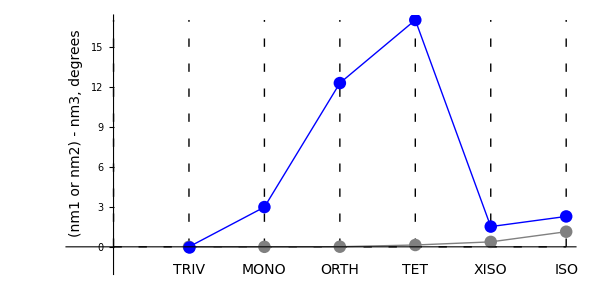

```mathematica
MatrixNote[Tmat]
Print["Node sequence is ",Σn/@domain[Σn]]
Print[" UforNM1 = ", MatrixForm[UforNM1]]
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm1,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm2col,Point[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}&/@domain[Σn]]},  (* line *)
{nm1col,Point[{#,ydiff[#,Tmat,Σn,nm1,nm3]/Degree}]&/@domain[Σn], (* points *)
                   Line[{#,ydiff[#,Tmat,Σn,nm1,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm1,nm3]/Degree}]&/@domain[Σn],
Text[Style["(nm1 or nm2) - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm1,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```

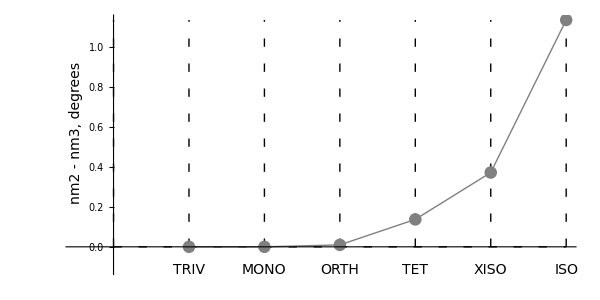

```mathematica
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm2,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm2col,Point[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm2,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm2,nm3]/Degree}]&/@domain[Σn],
Text[Style["nm2 - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm2,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```

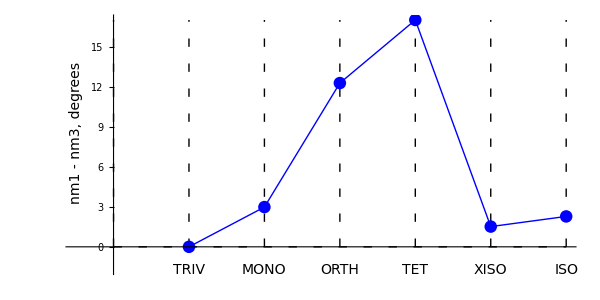

```mathematica
Graphics[{PointSize[.015],
{Dashing[{.01,.02}],
Line[{{0,0},{nMax[Σn],0}}],
Table[Line[{{n,0},{n,dymax[Tmat,Σn,nm1,nm3]/Degree}}],{n,0,nMax[Σn]}]},
{nm1col,Point[{#,ydiff[#,Tmat,Σn,nm1,nm3]/Degree}]&/@domain[Σn], (* points *)
                    Line[{#,ydiff[#,Tmat,Σn,nm1,nm3]/Degree}&/@domain[Σn]]},  (* line *)
Text[Style[Σn[#],14],{#,-0.1dymax[Tmat,Σn,nm1,nm3]/Degree}]&/@domain[Σn],
Text[Style["nm1 - nm3, degrees",14],{-.5,.5dymax[Tmat,Σn,nm1,nm3]/Degree},{0,0},{0,1}]
},
AspectRatio->1/2,ImageSize->600,Ticks->{None,Automatic},Axes->{None,True},GridLines-> None,AxesOrigin->{0,0}]
```